```mathematica
SetDirectory[NotebookDirectory[]]
<<mathutils.m
θtoϕ[a_,b_,c_]:=
Module[{l1,l2,θ1,θ2,θ3,l3,η1,η2,ee3,data,t,ϕ1sol,ϕ2sol,η11,η12,et},
l1 = 1;
l2 = 0.75;
l3 = 2;
θ1 = a;θ2=b;θ3=c;
η2=( l1*Sin[ϕ1]+l2*Sin[θ3]+l3*Sin[θ1]-(l1*Sin[ϕ2]+l2*Sin[θ2]));
η1 =( l1*Cos[ϕ1]+l2*Cos[θ3]+l3*Cos[θ1]-(l1*Cos[ϕ2]+l2*Cos[θ2]+l3));
ee3 = Numerator[Together[solveLinTrig2[{η1,η2},ϕ2][[2]]/.{Cos[ϕ1]-> (1-t^2)/(1+t^2),Sin[ϕ1]-> (2*t)/(1+t^2)}]];
et=Solve[ee3==0,t][[2]];
ϕ1sol ={ϕ1->  ArcTan[(1-t^2)/(1+t^2),(2*t)/(1+t^2)]/.et};
η11=η1/.ϕ1sol;
η12=η2/.ϕ1sol;
ϕ2sol = solveLinTrig2[{η11,η12},ϕ2][[1]];
Return[Flatten[{ϕ1sol,ϕ2sol}]];
]
```

/Users/Gautham/Desktop/Robotics Project/Mathematica

```mathematica
a=Import["deerstand.mat"]
```

{{{0.},{0.0000375},{0.000114063},{0.000205273},{0.000301978},{0.000400742},20989,{0.000371877},{0.000289454},{0.000196045},{0.0000985169},{-5.56152×10^-7},{-0.000100209}},2,{1}}
 |  |  |  |

```mathematica
th3=Flatten[a[[4]]];
th2=Flatten[a[[3]]];
dth2 = Flatten[a[[1]]];
dth3 = Flatten[a[[2]]];
th1=0;
dth1 = 0;
ϕ1list = {};
ϕ2list = {};
```

```mathematica
ϕ1list = {};
ϕ2list = {};
For[i=1,i≤ 21001,i++,
AppendTo[ϕ1list,ϕ1/.θtoϕ[0,th2[[i]],th3[[i]]]];
AppendTo[ϕ2list,ϕ2/.θtoϕ[0,th2[[i]],th3[[i]]]];
]
```

```mathematica
Export["ph1sm.csv",ϕ1list];
Export["ph2sm.csv",ϕ2list];
```

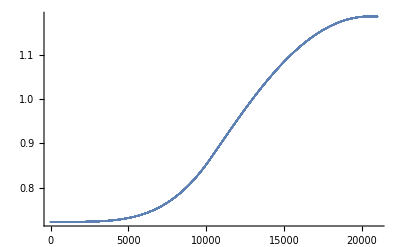

```mathematica
p1=ListPlot[ϕ1list]
```

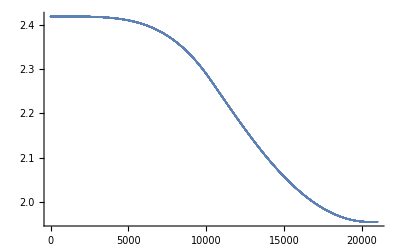

```mathematica
p2=ListPlot[ϕ2list]
```

```mathematica
dph1 = ConstantArray[0,21001];
dph2 = ConstantArray[0,21001];
For[i=1,i≤ 21000,i++,
AA=(Jϕθ/.{θ1[t]-> 0,θ2[t]-> th2[[i]],θ3[t]-> th3[[i]],ϕ1[t]-> ϕ1list[[i]],ϕ2[t]-> ϕ2list[[i]]}).{{0},{dth2[[i]]},{dth3[[i]]}};
dph1[[i]] = AA[[1]][[1]];
dph2[[i]] = AA[[2]][[1]];
]
```

```mathematica
t1 =  ConstantArray[0,21001];
t2 =  ConstantArray[0,21001];
t3 =  ConstantArray[0,21001];
For[i=1,i≤ 21000,i++,
ff=(Mθ/.{θ1[t]-> 0,θ2[t]-> th2[[i]],θ3[t]-> th3[[i]],ϕ1[t]-> ϕ1list[[i]],ϕ2[t]-> ϕ2list[[i]],θ1'[t]-> 0,θ2'[t]-> dth2[[i]],θ3'[t]-> dth3[[i]],ϕ1'[t]-> dph1[[i]],ϕ2'[t]-> dph2[[i]]}).{1,1,1}+(Cθ/.Idata/.mdata/.ldata/.{θ1[t]-> 0,θ2[t]-> th2[[i]],θ3[t]-> th3[[i]],ϕ1[t]-> ϕ1list[[i]],ϕ2[t]-> ϕ2list[[i]],θ1'[t]-> 0,θ2'[t]-> dth2[[i]],θ3'[t]-> dth3[[i]],ϕ1'[t]-> dph1[[i]],ϕ2'[t]-> dph2[[i]]}).{0,dth2[[i]],dth3[[i]]};
t1[[i]] = ff[[1]];
t2[[i]] = ff[[2]];
t3[[i]] = ff[[3]];
]
```

```mathematica
Export["tor1.csv",t1];
Export["tor2.csv",t2];
Export["tor3.csv",t3];
```